# Game of Life

The Game of Life is a two-dimensional cellular automaton invented by mathematician John Conway and can be considered as a simple model for behavior of a colony of organisms.

## Setting the scene

The scene on which the Game of Life takes place is a two-dimensional rectangular grid of cells. Each cell can be in one of two possible states: either alive - which is represented as 1, or dead - which is represented as 0.

“Make a 100 by 100 grid of random states and visualize it with colors - white for 0, black for 1:”

```mathematica
grid=RandomInteger[1,{100,100}];ArrayPlot[grid,Frame->False]
```

-Graphics-

## Defining the rules

The Game of Life is performed by evolution of the cells’ states in time. To carry out the evolution, rules of the evolution must be specified. The general principle is that successive state of a given cell depends on the states its neighboring cells and the cell itself had in the previous time step. Thus neighborhood of a cell needs to be specified.

“Visualize examples of neighborhoods on a grid. The black cells are considered neighbors of the pink cell in center:”

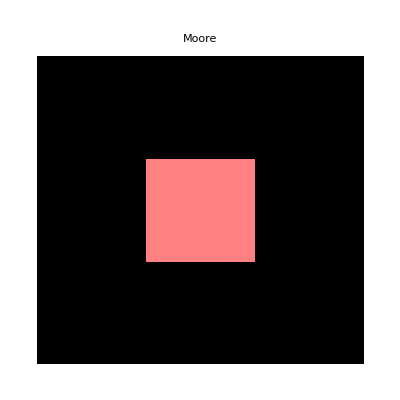
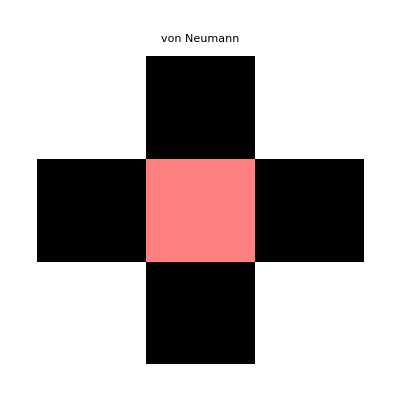

```mathematica
Row[{ArrayPlot[{{1,1,1},{1,Pink,1},{1,1,1}},PlotLabel->"Moore"],ArrayPlot[{{0,1,0},{1,Pink,1},{0,1,0}},PlotLabel->"von Neumann"]}]
```

We could specify any neighborhood, but the Game of Life uses Moore neighborhood. Having defined neighborhood of a cell we can define rules of evolution.

“Make a list of evolution rules. The first element in a rule is the state of a given cell, the second element is the number of cell’s neighbours which are alive. The new state of the cell is specified after the arrow:”

```mathematica
listOfRules={{1,2}->1,{1,3}->1,{0,3}->1,{_,_}->0}
```

{{1,2}→1,{1,3}→1,{0,3}→1,{_,_}→0}

## Evolution

The state of a cell at a given time depends on the sum of the states of its neighbours at the previous time step - the positions of the neighbours are not taken into consideration. It makes the Game of Life a totalistic cellular automaton. To calculate the evolution step in the game we have to count the number of neighbors for each cell on the grid.

“Calculate the number of neighbours for each cell on the grid:”

```mathematica
roll[m_,ind_]:=Join[m⟦ind;;⟧,m⟦;;ind-1⟧]
dirs={{-1,-1},{-1,1},{-1,2},{1,-1},{1,2},{2,-1},{2,1},{2,2}};
neighbors=Plus@@Map[Transpose[roll[Transpose[roll[grid,#⟦1⟧]],#⟦2⟧]]&,dirs];
ArrayPlot[neighbors,Frame->False]
```

-Graphics-

“Given the matrix of states of the cells and the matrix of the number of their neighbors calculate states of the cells in successive time point:”

```mathematica
ArrayPlot[Replace[Transpose[{grid, neighbors}, {3, 1, 2}], listOfRules, 2],Frame->False]
```

-Graphics-

“Make an animation of the grid evolution:”

```mathematica
Dynamic[ArrayPlot[grid=Last[CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},grid,{{0,1}}]]]]
```

## Patterns

There are many patterns which evolution in the Game of Life is particularly interesting

“Watch the evolution of patterns given as example:”

```mathematica
stillLives={
{{0,0,0,0,0},{0,0,1,0,0},{0,1,0,1,0},{0,0,1,0,0},{0,0,0,0,0}},
{{0,0,0,0,0,0},{0,0,1,1,0,0},{0,1,0,0,1,0},{0,0,1,1,0,0},{0,0,0,0,0,0}},
{{0,0,0,0,0},{0,1,1,0,0},{0,1,0,1,0},{0,0,1,0,0},{0,0,0,0,0}}
};
oscilltors={
{{0,0,0,0,0},{0,0,0,0,0},{0,1,1,1,0},{0,0,0,0,0},{0,0,0,0,0}},
{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,1,1,1,0},{0,1,1,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,1,1,0},{0,1,0,1,0,0,1,0,1,0},{0,0,0,1,1,1,1,0,0,0},{0,1,0,1,0,0,1,0,1,0},{0,1,1,0,0,0,0,1,1,0},{0,0,0,0,0,0,0,0,0,0}}
};
spaceShips={
{{0,0,0,0,0},{0,0,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,1,1,1,0},{0,0,0,0,0},{0,0,0,0,0}},
{{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,1,0,0,1,0},{0,1,0,0,0,0,0},{0,1,0,0,0,1,0},{0,1,1,1,1,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,1,1,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,1,0,1,0,0,1,0,1,0,0},{0,0,1,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,1,0,0},{0,0,0,1,1,0,0,1,1,0,0,0},{0,0,0,0,1,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}}
};
```

```mathematica
Partition[Map[Function[pat,
DynamicModule[{pattern=pat},
Dynamic[
ArrayPlot[
pattern=
Last[CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},pattern,{{0,1}}]]
]
]
]
],
Join[stillLives,oscilltors,spaceShips]
],3]//Grid
```

## Universal Computations

In 1982 John Conway and independently William Gosper have shown that the Game of Life is a universal Turing machine. The proof was based on the construction of logical gates NOT, AND and OR with the use of gliders.

Further Explorations

Investigate the theory of cellular automata

Investigate Matthew Cook proof that Rule 110 is Turing complete

Authorship information

Michal Sadowski

2017/06/23

ms304655@okwf.fuw.edu.pl